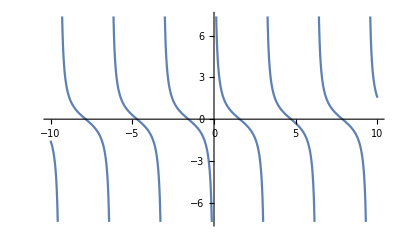

```mathematica
Plot[Cot[x], {x, -10, 10}]
```

Zeta Function

WolframAlphaQueryResults

```mathematica
Zeta[2]
```

π^2/6

```mathematica
Zeta[2]//N
```

1.64493

```mathematica
1+ 1/2^2+1/3^2//N
```

1.36111

```mathematica
Total[Table[1/k^2, {k, 1,10}]] //N //Timing
```

{0.000061,1.54977}

```mathematica
Timing[Zeta[2]]//N
```

{0.000044,1.64493}

```mathematica
sum = 0;
Timing[For[n = 1, n <= 10, n++, sum += 1/n^2]]
```

{0.00011,Null}

```mathematica
sum //N
```

1.54977

```mathematica
x[0] = 1;
For[n = 1, n <= 100, n++, x[n] = -0.5x[n -1] + Log[x[n - 1]]]
Table[x[n], {n , 1, 100}]
```

{-0.5,-0.443147+3.14159 ⅈ,1.37615+0.140134 ⅈ,-0.363626+0.0314132 ⅈ,-0.826098+3.03971 ⅈ,1.56044+0.3163 ⅈ,-0.315119+0.0418396 ⅈ,-0.988506+2.98867 ⅈ,1.64099+0.395886 ⅈ,-0.29691+0.0387819 ⅈ,-1.05741+2.99232 ⅈ,1.68359+0.414315 ⅈ,-0.291468+0.034138 ⅈ,-1.08028+3.00793 ⅈ,1.70205+0.411629 ⅈ,-0.290771+0.0314723 ⅈ,-1.08401+3.01804 ⅈ,1.70728+0.406604 ⅈ,-0.291154+0.0305011 ⅈ,-1.08287+3.02196 ⅈ,1.70774+0.403894 ⅈ,-0.291485+0.030293 ⅈ,-1.08165+3.02289 ⅈ,1.70728+0.402975 ⅈ,-0.291631+0.0303037 ⅈ,-1.08108+3.0229 ⅈ,1.70694+0.402802 ⅈ,-0.291673+0.0303391 ⅈ,-1.08091+3.02278 ⅈ,1.70679+0.402825 ⅈ,-0.291677+0.0303589 ⅈ,-1.08088+3.0227 ⅈ,1.70676+0.402863 ⅈ,-0.291674+0.0303659 ⅈ,-1.08089+3.02267 ⅈ,1.70675+0.402883 ⅈ,-0.291672+0.0303673 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303672 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.402891 ⅈ,-0.291671+0.030367 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.402891 ⅈ,-0.29167+0.0303668 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303668 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303668 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303668 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303668 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303668 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303668 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303668 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303668 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303668 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303668 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303668 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303668 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303668 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303668 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303668 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303668 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303668 ⅈ,-1.0809+3.02267 ⅈ,1.70676+0.40289 ⅈ,-0.291671+0.0303668 ⅈ}

```mathematica
ListPlot[Table[x[n], {n, 1, 100}], Joined->True]
```

-Graphics-

## Vector Fields, Vector and StreamLine Plots and Contour Plots

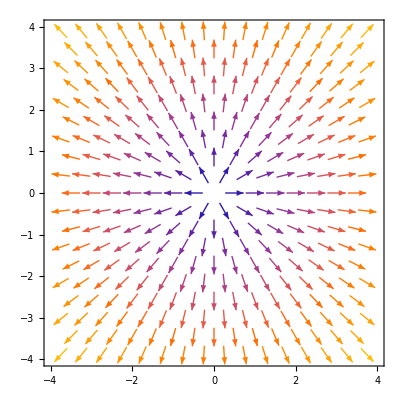

```mathematica
VectorPlot[{x, y}, {x,-4, 4}, {y, -4, 4}]
```

```mathematica
VectorPlot3D[{x, y, z}, {x, -4, 4}, {y, -4,4}, {z, -4, 4}, VectorScaling->"Linear"]
```

-Graphics3D-

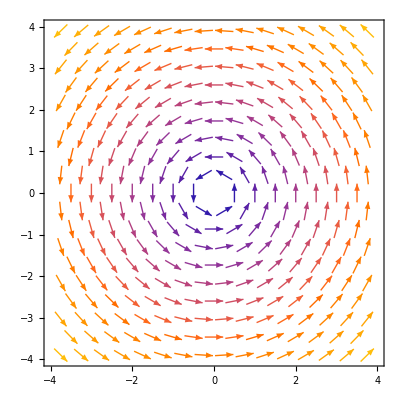

```mathematica
VectorPlot[{-y, x}, {x, -4, 4}, {y, -4, 4}]
```

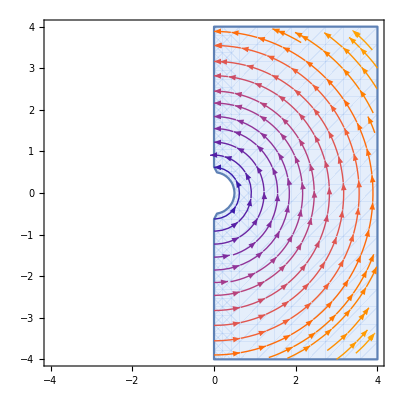

```mathematica
StreamPlot[{-y, x}, {x, -4, 4}, {y, -4, 4}, RegionFunction->Function[{x, y, vx, vy, n}, n> 0.5 && vy > 0]]
```

```mathematica
StreamDensityPlot[{-y, x}, {x, -4, 4}, {y, -4, 4}, RegionFunction->Function[{x, y, vx, vy, n}, n> 0.5 && vy > 0]]
```

-Graphics-

```mathematica
StreamDensityPlot[{x,y}, {x, -4, 4}, {y, -4, 4}]
```

-Graphics-

```mathematica
VectorPlot3D[{-y, x, z}, {x, -4, 4}, {y, -4, 4},{z, -4, 4}]
```

-Graphics3D-

```mathematica
StreamPlot[{x/((√(x^2+y^2))^3), y/((√(x^2+y^2))^3)}, {x, -5, 5}, {y, -5, 5}, RegionFunction->Function{x, y, vx, vy, n}, n > 0.1]
```

StreamPlot::nonopt: Options expected (instead of n>0.1) beyond position 3 in StreamPlot[{x/(√(Power[«2»]+Power[«2»]))^3,y/(√(Power[«2»]+Power[«2»]))^3},{x,-5,5},{y,-5,5},RegionFunction→Function {x,y,vx,vy,n},n>0.1]. An option must be a rule or a list of rules.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

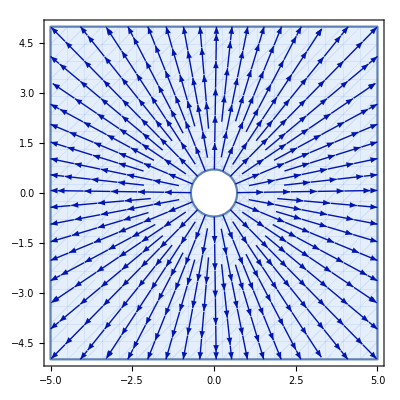

```mathematica
StreamPlot[{x/((√(x^2+y^2))^3),y/((√(x^2+y^2))^3)},{x,-5,5},{y,-5,5},RegionFunction->Function [{x,y,vx,vy,n},n <2]]
```

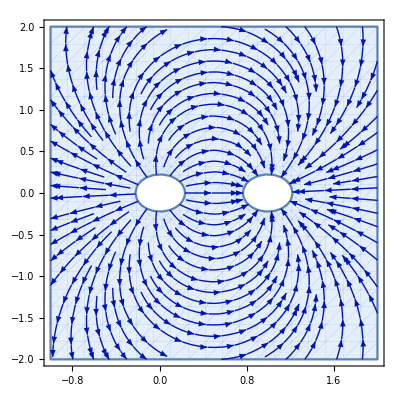

```mathematica
fieldLines = StreamPlot[{x/r^3- (x - 1)/r1^3, y/r^3- y/r1^3}/.r->√(x^2+y^2)/.r1->√((x-1)^2+y^2), {x, -1, 2}, {y, -2, 2}, RegionFunction->Function[{x, y, vx, vy, n}, n< 20 ]]
```

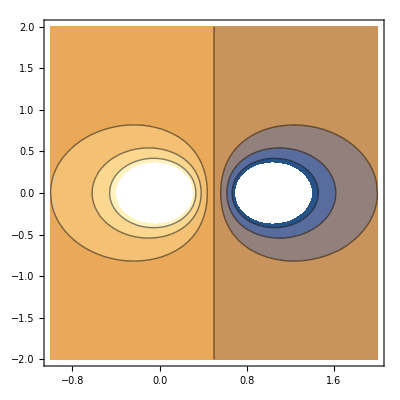

```mathematica
equiPotential = ContourPlot[{1/r - 1/r1}/.r->√(x^2+y^2)/.r1->√((x-1)^2+y^2), {x, -1, 2}, {y, -2, 2}]
```

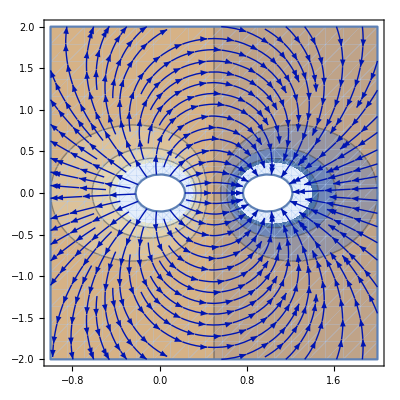

```mathematica
Show[equiPotential, fieldLines]
```

1-Cos[θ]

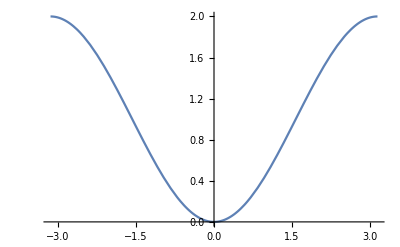

```mathematica
ν = 1 - Cos[θ]
Plot[ν, {θ, -π, π}]
```

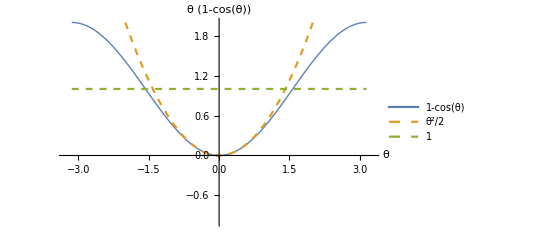

```mathematica
Plot[{1 - Cos[θ], θ^2/2, 1}, {θ, -π, π}, PlotRange->{-1,2 }, AxesLabel->{Style[θ, 15], Style[ν(θ), 15]}, AxesStyle->Thick, TicksStyle->Directive["Label", 14], PlotLegends->"Expressions", PlotStyle->{Thick, Dashed, Dashed}]
```

```mathematica
Pi/2 //N
```

1.5708

```mathematica
Plot[{-γ/Cos[θ]^2 x^2+ Tan[Θ]x, + 1, -Tan[ϕ]x + 1, 0}/.{γ-> 1, ϕ->π/6,θ->π/3 }, {x, 0, 1}]
```

-Graphics-

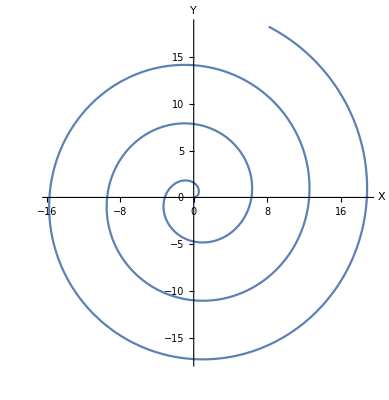

```mathematica
ParametricPlot[{T Cos[T], T Sin[T]},{T, 0, 20}, AxesLabel->{"X", "Y"}]
```

# Quiz 1

```mathematica
Manipulate[Plot[{x^(1/n), Log[x]}, {x, 0, 20}], {{n, 2.5}, 1, 20, 0.15}]
```

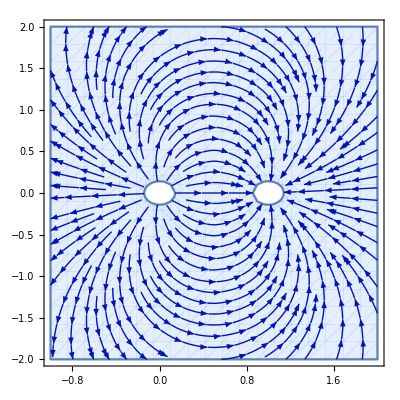

```mathematica
StreamPlot[{x/r^3- (x-1)/(r1^3), y/r^3- y/r1^3}/.r->Sqrt[(x^2)+(y^2)]/.r1->Sqrt[(x -1)^2+y^2], {x,-1,2},{y, -2,2}, RegionFunction->Function[{x,y,vx,vy,n},n<50]]
```

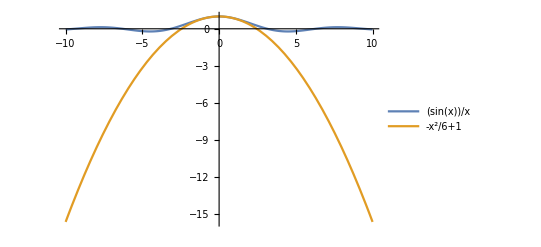

```mathematica
Plot[{Sin[x]/x, -x^2/6+ 1}, {x, -10, 10}, PlotLegends->"Expressions"]
```

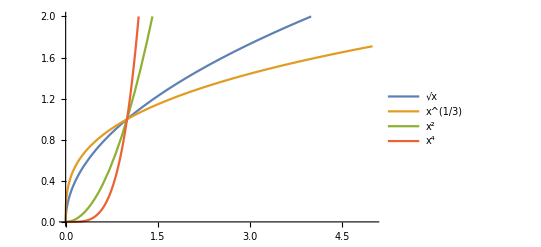

```mathematica
Plot[{x^(1/2),x^(1/3),x^2,x^4}, {x, 0, 5}, PlotRange->{0,2}, PlotLegends->"Expressions"]
```

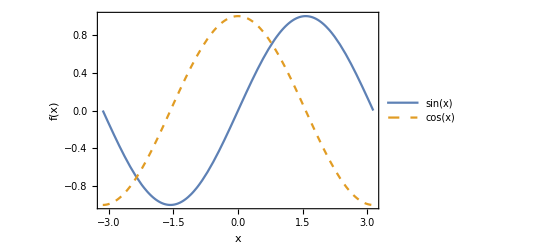

```mathematica
Plot[{Sin[x], Cos[x]}, {x, -π, π}, PlotLegends->"Expressions", PlotStyle->{Thick, Dashed}, Frame->True, FrameLabel->{x, "f(x)"}]
```

```mathematica
NSolve[x =101, x]
```

{}

```mathematica
NSolve[{Log[x] -  x^(1/3)== 0}, x]
```

{}